# -Graphics-

# Parallel Programming

## In Wolfram Language

## Outline

Introduction

The basics

Automatic parallelisation

Parallel analogues

Manual control

Sharing state

Tuning

Remote computation

Summary

## Introduction

#### What is parallelisation?

Parallelisation is the ability to split a single task into multiple instructions that can be done simultaneously by several “workers” (subkernels).

```mathematica
CellPrint[
ExpressionCell[
With[
{
st1=Red,
st2=Orange,
st3=Blue
},
Graph[
{
Style["Task Manager"->"Results",st1],Style["Task Manager"->"Worker 1",st2],Style["Task Manager"->"Worker 2",st2],Style["Task Manager"->"Worker 3",st2],Style["Task Manager"->"Worker 4",st2],Style["Worker 1"->"Task Manager",st3],Style["Worker 2"->"Task Manager",st3],Style["Worker 3"->"Task Manager",st3],Style["Worker 4"->"Task Manager",st3]
},
PlotTheme->"IndexLabeled",
VertexLabels->Placed["Name", Center],
VertexCoordinates->{"Task Manager"->{1,1},"Results"->{2.5,1},"Worker 1"->{0.4,1.8},"Worker 2"->{1.6,1.8},"Worker 3"->{0.4,0.2},"Worker 4"->{1.6,0.2}},
VertexSize->0.5,
EdgeLabels->{"Task Manager"->"Results"->Placed["Collected answers", 0.4],"Task Manager"->"Worker 1"->Placed["Instructions", 0.6],"Task Manager"->"Worker 2"->Placed["Instructions", 0.6],"Task Manager"->"Worker 3"->Placed["Instructions", 0.6],"Task Manager"->"Worker 4"->Placed["Instructions", 0.6],"Worker 1"->"Task Manager"->Placed["Answers", 0.6],"Worker 2"->"Task Manager"->Placed["Answers", 0.6],"Worker 3"->"Task Manager"->Placed["Answers", 0.6],"Worker 4"->"Task Manager"->Placed["Answers", 0.6]},
PerformanceGoal->"Quality",
ImageSize->500
]
],
"Output",
GeneratedCell -> False
]
]
```

-Graphics-

When performing a parallelised task, Mathematica will launch as many subkernels as there are processor cores on your machine:

```mathematica
$ProcessorCount
```

#### When should you do it?

Parallelisation is good for:

Long/heavy computations

Tasks that can be split into subtasks

Tasks with small inputs or outputs

#### How much will it help?

Each worker will have some overhead when sending or receiving instructions, so choosing whether or not to parallelise is always a balancing act.

Any data required for a task will be sent to workers sequentially. It is therefore advisable to send each worker a reference to the data, rather than the data itself.

Amdahl's Law: “The overall performance improvement gained by optimising a single part of a system is limited by the fraction of time that the improved part is actually used.”

## The Basics

#### Working with kernels

LaunchKernels launches all of the default parallel subkernels (if they are not launched already):

```mathematica
LaunchKernels[]
```

Evaluating it again will produce an error:

```mathematica
LaunchKernels[]
```

Kernels gives a list of all running parallel subkernels:

```mathematica
Kernels[]
```

AbortKernels aborts all running parallel subkernels:

```mathematica
AbortKernels[]
```

CloseKernels terminates all running parallel subkernels:

```mathematica
CloseKernels[]
```

#### Global variables

$KernelCount gives the number of running parallel subkernels:

```mathematica
$KernelCount
```

$ProcessorCount gives the number of processor cores available on the system that can run a Wolfram kernel:

```mathematica
$ProcessorCount
```

Other related variables:

```mathematica
?$*Kernel*
```

```mathematica
?$*Processor*
```

#### Parallel kernel configuration

To access the parallel kernel configuration interface, go to Evaluation ▶ Parallel Kernel Configuration…:

```mathematica
GraphicsRow[
Flatten[
Map[
Image[Import[#]]&,
{"Preferences_Windows.png","Preferences_Mac.png"}
]
],
ImageSize -> Full
]
```

-Graphics-

## Automatic Parallelisation

Wolfram Language has several built-in functions designed to parallelise specific tasks. Where no such function exists for a particular task, it may still be possible to parallelise automatically.

#### Parallelize

Parallelize is an all-purpose tool that attempts to parallelise whatever computation is given to it:

```mathematica
LaunchKernels[4]
```

```mathematica
Parallelize[Table[Length[FactorInteger[10^50+n]],{n,20}]]
```

In the case of Table, it would make more sense to use the built-in parallel version, ParallelTable:

```mathematica
ParallelTable[Length[FactorInteger[10^50+n]],{n,20}]
```

Not all functions are parallelisable:

```mathematica
Parallelize[Integrate[1/x,x]]
```

#### ParallelEvaluate

ParallelEvaluate will run a copy of the same computation on each subkernel. This can be useful for checking or averaging results.

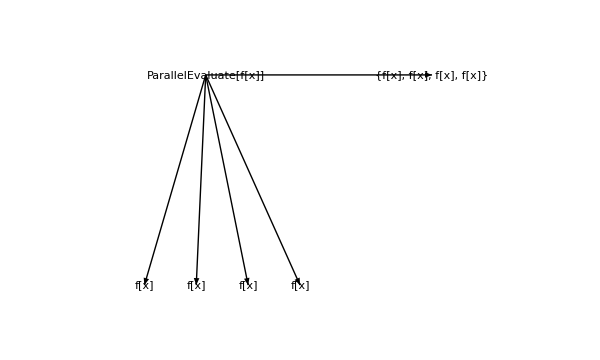

```mathematica
CellPrint[
ExpressionCell[
diagram["ParallelEvaluate[f[x]]",{"f[x]", "f[x]", "f[x]", "f[x]"},"{f[x], f[x], f[x], f[x]}"],
"Output",
GeneratedCell -> False
]
]
```

Get the IDs of all running subkernels:

```mathematica
kernelIDs = ParallelEvaluate[$KernelID]
```

Generate a random number for each subkernel:

```mathematica
ParallelEvaluate[Labeled[Framed[RandomReal[]], $KernelID]]
```

Choose a specific subkernel to evaluate with:

```mathematica
ParallelEvaluate[Labeled[Framed[RandomReal[]], $KernelID], kernelIDs[[1]]]
```

Symbols defined in a global context are distributed among subkernels automatically:

```mathematica
f[n_]:=Labeled[Framed[n^2], $KernelID];

ParallelEvaluate[f[10]]
```

## Parallel Analogues

Wolfram Language has several “parallel versions” of built-in functions.

#### ParallelTable

ParallelTable is the parallel version of Table. It automatically distributes iterations of a task across workers.

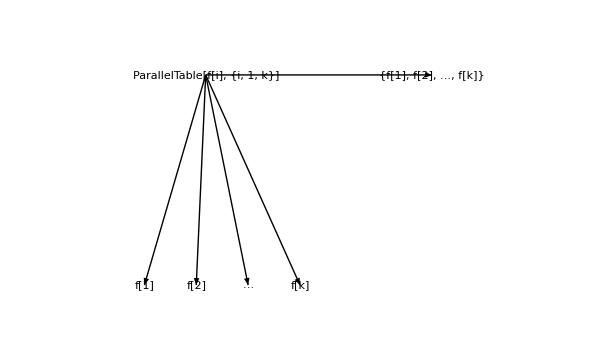

```mathematica
CellPrint[
ExpressionCell[
diagram["ParallelTable[f[i], {i, 1, k}]",{"f[1]", "f[2]", "…", "f[k]"},"{f[1], f[2], …, f[k]}"],
"Output",
GeneratedCell -> False
]
]
```

Iterate twice as many times as there are available subkernels:

```mathematica
Table[Labeled[Framed[i^2], $KernelID],{i,2*$KernelCount}]
```

```mathematica
ParallelTable[Labeled[Framed[i^2], $KernelID],{i,2*$KernelCount}]
```

For short computations, the overhead involved in ParallelTable makes it slower than Table:

```mathematica
Table[i^2,{i,10^4}];//RepeatedTiming
```

```mathematica
ParallelTable[i^2,{i,10^4}];//RepeatedTiming
```

For longer computations, the overhead becomes less important:

```mathematica
Table[Length[FactorInteger[10^50+n]],{n,20}];//RepeatedTiming
```

```mathematica
ParallelTable[Length[FactorInteger[10^50+n]],{n,20}];//RepeatedTiming
```

Compare timings for Table and ParallelTable for increasingly lengthy computations:

```mathematica
With[
{
tableTimings = Table[First[AbsoluteTiming[Table[FactorInteger[2^i+1], {i, 1, j}];]], {j, 10, 150, 5}],
parallelTableTimings = Table[First[AbsoluteTiming[ParallelTable[FactorInteger[2^i+1], {i, 1, j}];]], {j, 10, 150, 5}]
},
ListLinePlot[
{tableTimings, parallelTableTimings},
Frame -> True,
FrameLabel -> {None, "Timing"},
PlotLegends -> {"Table", "ParallelTable"},
FrameTicks -> None,
ImageSize -> 500
]
]
```

#### ParallelDo

ParallelDo is the parallel version of Do. It performs the same calculation as ParallelTable, but without returning a result:

```mathematica
ParallelTable[i,{i,4}]
```

```mathematica
ParallelDo[i,{i,4}]
```

Adding a pause emphasises the difference between Do and ParallelDo:

```mathematica
Do[{Pause[1];Print[i]},{i,4}]//AbsoluteTiming
```

```mathematica
ParallelDo[{Pause[1];Print[i]},{i,4}]//AbsoluteTiming
```

Note that parallel tasks may be evaluated out of sequence:

```mathematica
ParallelDo[{Print[i]},{i,10}]
```

#### ParallelSum

ParallelSum is the parallel version of Sum:

```mathematica
Sum[i^2,{i,1000}]
```

```mathematica
ParallelSum[i^2,{i,1000}]
```

```mathematica
Sum[EulerPhi[i], {i, 10^6}];//RepeatedTiming
```

```mathematica
ParallelSum[EulerPhi[i], {i, 10^6}];//RepeatedTiming
```

#### ParallelProduct

ParallelProduct is the parallel version of Product:

```mathematica
Product[i,{i,100}]
```

```mathematica
ParallelProduct[i,{i,100}]
```

```mathematica
Product[EulerPhi[i], {i, 10^6}];//RepeatedTiming
```

```mathematica
ParallelProduct[EulerPhi[i], {i, 10^6}];//RepeatedTiming
```

#### ParallelMap

ParallelMap is the parallel version of Map:

```mathematica
Map[f, Range[1, $KernelCount]]
```

```mathematica
ParallelMap[f, Range[1, $KernelCount]]
```

#### ParallelArray

ParallelArray is the parallel version of Array:

```mathematica
Array[f[#1, #2]&, {3, 2}]
```

```mathematica
ParallelArray[f[#1, #2]&, {3, 2}]
```

#### ParallelCombine

Although not directly related to an existing built-in function, ParallelCombine is useful for creating your own custom parallel functions.

ParallelCombine deals with “chunks” of a task in parallel, then applies a secondary function (Join, by default) to the result.

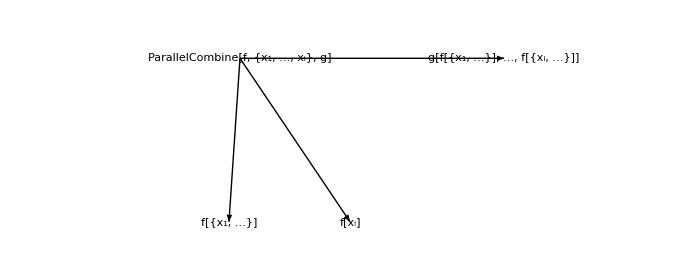

```mathematica
CellPrint[
ExpressionCell[
diagram["ParallelCombine[f, {x_1, …, x_i}, g]",{"f[{x_1, …}]", "f[x_i]"},"g[f[{x_1, …}], …, f[{x_i, …}]]",
ImageSize -> 700,
AspectRatio -> 0.4
],
"Output",
GeneratedCell -> False
]
]
```

Apply two functions to a list:

```mathematica
ParallelCombine[p,Range[2*$KernelCount], q]
```

Create a parallel version of MapThread:

```mathematica
parallelMapThread[function_,args_List]:=ParallelCombine[MapApply[function, #]&,Transpose[args]];

parallelMapThread[p,{{"a", "b", "c"}, {"d", "e", "f"}, {"g", "h", "i"}}]
```

The built-in function is significantly faster when threading a small number of lists:

```mathematica
MapThread[Plus, RandomInteger[{-10, 10}, {3, 10^4}]];//RepeatedTiming
```

```mathematica
parallelMapThread[Plus, RandomInteger[{-10, 10}, {3, 10^4}]];//RepeatedTiming
```

But this is not so when threading many lists:

```mathematica
MapThread[Plus, RandomInteger[{-10, 10}, {10^5, 100}]];//RepeatedTiming
```

```mathematica
parallelMapThread[Plus, RandomInteger[{-10, 10}, {10^5, 100}]];//RepeatedTiming
```

Note that ParallelCombine should generally only be used—as you may have guessed from the diagram—for operations where the output does not depend on the batching of the inputs (e.g. operations like addition or multiplication).

## Manual Control

#### ParallelTry

ParallelTry works like ParallelMap, but only returns the first result that has finishing computing.

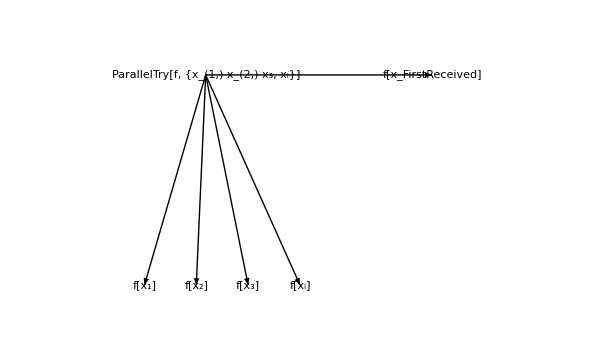

```mathematica
CellPrint[
ExpressionCell[
diagram["ParallelTry[f, {x_(1,) x_(2,) x_3, x_i}]",{"f[x_1]", "f[x_2]", "f[x_3]", "f[x_i]"}, "f[x_FirstReceived]"],
"Output",
GeneratedCell -> False
]
]
```

Return the result with the shortest pause, even though it was last to be evaluated:

```mathematica
ParallelTry[(Pause[#];#)&,{4,3,2,1}]
```

Find the next prime after 9 899 999 999, returning the results from the first three subkernels:

```mathematica
With[
{start = 9899999999},
ParallelTry[
(Pause[1]; Labeled[Framed[NextPrime[#]],$KernelID])&,
ConstantArray[start, $KernelCount],
3
]
]
```

#### ParallelSubmit, WaitNext and WaitAll

ParallelSubmit submits a task to the next available subkernel, but does not evaluate it. WaitNext and WaitAll can then be used to evaluate and return the results.

Submit several tasks to subkernels:

```mathematica
tasks=Table[ParallelSubmit[{i},Length[FactorInteger[2^i-1]]],{i,181,184}]
```

Return the first result:

```mathematica
{firstResult,evalObjectID,otherTasks}=WaitNext[tasks]
```

Return the remaining results:

```mathematica
WaitAll[otherTasks]
```

Watch the scheduling of evaluations while they are running:

```mathematica
With[
{base=10^1000,r=10^10},
evals=Table[
ParallelSubmit[
(
While[!PrimeQ[p=RandomInteger[{base,base+r}]],Null];
p-base
)
],
{$KernelCount}
];
PrintTemporary[evals];
WaitAll[evals]
]
```

## Sharing State

#### DistributeDefinitions

DistributeDefinitions distributes the definition(s) of a symbol to all parallel subkernels, giving each one a local copy. (Recall that for symbols defined in the global context, this is done automatically.)

Since f is defined globally, ParallelEvaluate evaluates it in parallel:

```mathematica
f[n_] := Labeled[Framed[n], $KernelID];
Context[f]
```

```mathematica
ParallelEvaluate[f[$KernelID]]
```

Since myContext`f only exists in one context, it is evaluated sequentially:

```mathematica
myContext`f[n_] := Labeled[Framed[n, FrameStyle -> Blue], $KernelID];
Context[myContext`f]
```

```mathematica
ParallelEvaluate[myContext`f[$KernelID]]
```

After distributing its definitions, myContext`f evaluates in parallel:

```mathematica
DistributeDefinitions[myContext`f];

ParallelEvaluate[myContext`f[$KernelID]]
```

To remove a distributed definition, clear and redistribute it:

```mathematica
ClearAll[myContext`f];
DistributeDefinitions[myContext`f];
```

```mathematica
myContext`f[n_] := Labeled[Framed[n, FrameStyle -> Blue], $KernelID];
ParallelEvaluate[myContext`f[$KernelID]]
```

#### SetSharedVariable

SetSharedVariable distributes the definition(s) of a symbol among subkernels and synchronises them (via the master kernel).

Consider a global symbol, val. Without sharing, each subkernel updates its own copy of the symbol:

```mathematica
val = 1;
```

```mathematica
ParallelEvaluate[val++]
```

With sharing, the definition of val is synchronised:

```mathematica
SetSharedVariable[val];
ParallelEvaluate[val++]
```

Use $SharedVariables to see all the variables currently being shared:

```mathematica
$SharedVariables
```

Use UnsetShared to unshare variables:

```mathematica
UnsetShared[val];
$SharedVariables
```

Note that unsharing a variable does not clear its definition:

```mathematica
val
```

#### SetSharedFunction

SetSharedFunction is like SetSharedVariable, but for functions.

Without sharing, each subkernel updates val with its own copy of g:

```mathematica
val = 1;
g[] := val++;
```

```mathematica
ParallelEvaluate[g[]]
```

With sharing, the definition of g (and therefore val) is synchronised:

```mathematica
val = 1;
g[] := val++;
SetSharedFunction[g];
```

```mathematica
ParallelEvaluate[g[]]
```

Use $SharedFunctions to see all currently shared functions:

```mathematica
$SharedFunctions
```

Use UnsetShared to unshare functions:

```mathematica
UnsetShared[g];
$SharedFunctions
```

#### CriticalSection

CriticalSection specifies a piece of code (known as a critical section) that should only be evaluated by one subkernel at a time.

Sharing read/write operations among subkernels may lead to unexpected results:

```mathematica
n=m=0;
SetSharedVariable[n, m];
ParallelEvaluate[n++; m=n]
```

CriticalSection ensures that the operation is evaluated “safely”:

```mathematica
n=m=0;
Clear[lockVariable];
ParallelEvaluate[CriticalSection[lockVariable, n++; m=n]]
```

The locking method works by writing the current subkernel’s ID to the lock variable, performing the operation, then clearing the lock variable.

#### ParallelNeeds

ParallelNeeds runs the Needs function in all parallel subkernels:

```mathematica
Needs["ComputerArithmetic`"];
ParallelNeeds["ComputerArithmetic`"];

ParallelEvaluate[ComputerNumber[2]]
```

## Tuning

When parallel computing, the parallelisation method can be tuned (with the default being Automatic—a compromise between overhead and load balancing).

#### Small grain

A smaller batch size means a more efficient use of CPU, at the cost of more communication between workers.

The "FinestGrained" method will break the computation into the smallest possible calculations:

```mathematica
BlockRandom[Parallelize[Map[Pause, RandomReal[1, 12]]];//RepeatedTiming]
```

```mathematica
BlockRandom[Parallelize[Map[Pause, RandomReal[1, 12]],Method -> "FinestGrained"];//RepeatedTiming]
```

This method is suitable for computations involving few calculations, whose evaluations take different amounts of time. It leads to higher overhead, but maximises load balancing.

#### Large grain

A larger batch size means a less efficient use of CPU, but also less communication needed.

The "CoarsestGrained" method will break the computation into as many pieces as there are available kernels:

```mathematica
ParallelSum[N[i],{i,10^6}]//RepeatedTiming
```

```mathematica
ParallelSum[N[i],{i,10^6},Method->"CoarsestGrained"]//RepeatedTiming
```

```mathematica
Parallelize[Map[Labeled[Framed[#],$KernelID]&,Range[100]],Method->"CoarsestGrained"]//RepeatedTiming
```

```mathematica
Parallelize[Map[Labeled[Framed[#],$KernelID]&,Range[100]], Method->"FinestGrained"]//RepeatedTiming
```

This method is suitable for computations involving many calculations, all of which take the same amount of time. It minimises overhead, but does not provide any load balancing.

#### Custom grain size

Choosing a custom grain size can mean getting the best of both worlds.

The "EvaluationsPerKernel"→e method will break the computation into at most e evaluations per kernel:

```mathematica
Parallelize[Table[Labeled[Framed[i],$KernelID],{i,20}],Method->"EvaluationsPerKernel"->2]
```

The "ItemsPerEvaluation"→m method will break the computation into evaluations of at most m calculations each:

```mathematica
Parallelize[Table[Labeled[Framed[i],$KernelID],{i,20}],Method->"ItemsPerEvaluation"->3]
```

## Remote Computation

#### RemoteEvaluate

RemoteEvaluate evaluates an expression on a specified remote kernel.

Connect to the Wolfram Cloud and see the server URL:

```mathematica
CloudConnect[]
```

```mathematica
$CloudBase
```

Get details about the server:

```mathematica
RemoteEvaluate[$CloudBase,{$MachineName,$ProcessID,$Version}]//Column
```

Perform a calculation:

```mathematica
RemoteEvaluate[$CloudBase, PrimeQ[2^1279-1]]
```

#### KernelConfiguration

KernelConfiguration is a wrapper that is used to specify configuration options for parallel kernels for RemoteEvaluate and LauchKernels which override the default kernel settings.

For example specify a Kernel Command to run a different kernel that default:

```mathematica
RemoteEvaluate["localhost",{$MachineName,$ProcessID,$Version, $KernelCount}]//Column
```

```mathematica
RemoteEvaluate[KernelConfiguration["localhost", "KernelCommand"->FileNameJoin[{ParentDirectory[$InstallationDirectory], "12.3", "WolframKernel.exe"}]],{$MachineName,$ProcessID,$Version}]//Column
```

#### Wolfram Lightweight Grid client

The Lightweight Grid client is a system for launching and managing remote Mathematica kernels.

Launch two local kernels:

```mathematica
CloseKernels[];
LaunchKernels[2]
```

Launch two remote kernels that have been configured with the Lightweight Grid client:

```mathematica
LaunchKernels["lwg://wreljarvis.wolfram.com",2]
```

All four kernels are now available for computation:

```mathematica
Kernels[]
```

```mathematica
CloseKernels[]
```

#### Batch computation

Batch computation can be done with Amazon Web Services (AWS). This is just one of many external services available:

```mathematica
$Services
```

Pros:

Remote; can be left to run in the background

Little setup required

Can run as many tasks as you want

Cons:

Computations may not start immediately

Requires a subscription (where the cost will depend on the level of service)

Using this service requires user credentials. Here are some example inputs and their outputs:

```mathematica
ServiceConnect["AWS", "New"]
```

-Graphics-

```mathematica
env = RemoteBatchSubmissionEnvironment[
"AWSBatch",
<|
"JobQueue"->"arn:aws:batch:us-east-2:337830956718:job-queue/WolframJobQueue-7e156ef3cfdca27",
"JobDefinition"->"arn:aws:batch:us-east-2:337830956718:job-definition/WolframJobDefinition-beeadc6fbadaf65:1",
"IOBucket"->"mywolframbatchstack-wolframjobdatabucket-yz8qoysjpko"
|>
]
```

-Graphics-

```mathematica
job = RemoteBatchSubmit[env,1988^1988]
```

-Graphics-

```mathematica
job["JobStatus"]
```

-Graphics-

```mathematica
job["JobStatus"]
```

-Graphics-

```mathematica
job["EvaluationResult"]//Short
```

-Graphics-

#### Background tasks

Tasks can be scheduled to run the background.

SessionSubmit / LocalSubmit / CloudSubmit

ScheduledTask / ContinuousTask

## Summary

Things to consider when parallel computing:

Size of the task

Ability to split the task into subtasks

Size of inputs/outputs

Independent vs sequential subtasks

Local vs remote computation

## Resources

#### Parallel computing

Overview: Parallel Computing Tools User Guide

Guide: Parallel Computing

Tutorial: Configuring Kernels for Parallel Computing

Guide: Concurrency

Guide: Resource Sharing in Parallel Computing

Tutorial: Virtual Shared Memory

How to: Connect to a Remote Kernel

Guide: Remote Computation

Guide: Managing Remote and Parallel Kernels

Tutorial: Introduction to the Wolfram Lightweight Grid System

Guide: Remote Batch Jobs

Workflow: Remote Batch Computation

Service connection: AWS

Guide: Background & Scheduled Tasks

#### Learning Wolfram Language

Wolfram U: Introduction to Notebooks

An Elementary Introduction to the Wolfram Language

Fast Introduction for Programmers

Wolfram U: Study Groups: Wolfram Language Tutorials

Wolfram Cloud

Latest Wolfram Language features:

Wolfram Language & Mathematica Releases

Stephen Wolfram Blog: "Launching Version 13.2"

What’s New in Mathematica 13

## Thank you for listening!

## Tuesday, June 16, 2026 · 15:00 BST

## Wolfram Language for Python Users

## Register: https://wolfr.am/1EC6pDWS3

## -Graphics-

### Initialisation

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[], "AdditionalFiles"}]];
```

```mathematica
CloseKernels[];
```

```mathematica
ClearAll[diagram];

Options[diagram] = DeleteDuplicates[
	Join[
		{
			FontSize -> 14,
			"ArrowSize" -> 0.03
			,
			PlotRange -> {{-4, 9}, {-0.2, 1.2}},
			AspectRatio -> 0.6,
			ImageSize -> 600
		},
		Options[Graphics]
	]
];

diagram[head_String, leaf_List, out_String, options : OptionsPattern[]] := Module[
	{ts},
	ts[expr_, pos_] := Text[
		Framed[
			Style[expr, FontFamily -> "Courier", FontSize -> OptionValue[FontSize]],
			Background -> LightYellow,
			RoundingRadius -> 5
		],
		pos
	];
	Graphics[
		{
			Table[
				{
					Arrowheads[{0, -OptionValue["ArrowSize"], OptionValue["ArrowSize"], 0}],
					Arrow[{{0, 1}, {5.5 / Length @ leaf * i - 3, 0}}],
					ts[leaf[[i]], {5.5 / Length @ leaf * i - 3, 0}]
				},
				{i, 1, Length @ leaf}
			],
			Arrowheads[{{OptionValue["ArrowSize"], 0.6}}],
			Arrow[{{0, 1}, {6, 1}}],
			ts[head, {0, 1}],
			ts[out, {6, 1}]
		},
		Sequence @@ FilterRules[Join[{options}, Options[diagram]], Options[Graphics]]
	]
];
```